```mathematica
repeats=1;
conc=Table[{0,0.1,0.25,0.5,1,2.5,5,10},{i,1,repeats}];
```

```mathematica
proteinDilution=1; (*protein dilution factor before addition to 100μl well*)
proteinConc=4/proteinDilution; (*mg·ml^-1 from bradford*)
lysateDilutionInWell=100/20; (*20μl in 100μl assay*)
pathLength=0.26; (*10μl well volume*)
NADHExt=6.22 (*mM^-1 cm^-1*);
```

```mathematica
rangeCheck[r_]:=Module[{},Manipulate[range[r]={p⟦1⟧,q⟦1⟧};Show[dataPlots⟦r⟧,Epilog->{Gray,Opacity[0.2],Rectangle[{p⟦1⟧,-1},{q⟦1⟧,2}]}],{{p,{0,0}},Locator,Appearance->None},{{q,{data⟦1,-1,1⟧,0}},Locator,Appearance->None}]]
```

```mathematica
(*Quiet[Table[rangeCheck[i],{i,Length[dataPlots]}]]*)
```

```mathematica
rangeFolder="linearRanges";
```

|

{{0,3.16},{0.35,3.35},{0.38,3.53},{0.61,3.67},{0,2.08},{1.25,2.93},{0,1.51},{1.27,2.87}}

```mathematica
rates=-Table[D[fits[[i]][x],x],{i,1,Length[fits]}]*(lysateDilutionInWell*proteinDilution/(NADHExt*pathLength*proteinConc))
```

{0.00464656,0.012946,0.0239746,0.042379,0.0756601,0.110921,0.110367,0.104028}

```mathematica
(*Export[FileNameJoin[{dir,folder,rangeFolder,rangeFileName}],ranges]*)
```

|

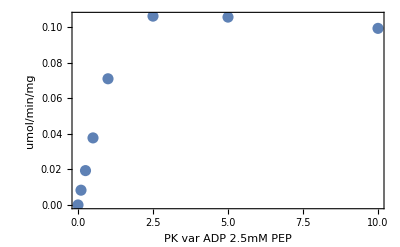

```mathematica
Pane[
,
Full,Alignment->Center]
```

```mathematica
headings={{"mM","V (umol/min/mg)"}};
```

PK var ADP 2.5mM PEP | 
mM | V (umol/min/mg)
0 | 0.
0.1 | 0.00829943
0.25 | 0.019328
0.5 | 0.0377324
1 | 0.0710136
2.5 | 0.106275
5 | 0.10572
10 | 0.0993819

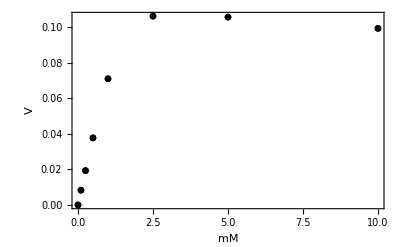

```mathematica
dataForExport=Join[headings,SortBy[rateData,First]];
```

### Data formatting:

```mathematica
allDataHeadings={{"PEP","ADP","PYR","ATP","F16BP","V(umol/min/mg)"}};
```

#### vary PEP

```mathematica
dataFormatted={#[[1]],0,0,0,0,#[[2]]}&/@SortBy[rateData,First]
```

{{0,0,0,0,0,0.},{0.1,0,0,0,0,0.00829943},{0.25,0,0,0,0,0.019328},{0.5,0,0,0,0,0.0377324},{1,0,0,0,0,0.0710136},{2.5,0,0,0,0,0.106275},{5,0,0,0,0,0.10572},{10,0,0,0,0,0.0993819}}

#### vary ADP

```mathematica
dataFormatted={0,#[[1]],0,0,0,#[[2]]}&/@SortBy[rateData,First]
```

{{0,0,0,0,0,0.},{0.1,0,0,0,0,0.00829943},{0.25,0,0,0,0,0.019328},{0.5,0,0,0,0,0.0377324},{1,0,0,0,0,0.0710136},{2.5,0,0,0,0,0.106275},{5,0,0,0,0,0.10572},{10,0,0,0,0,0.0993819}}

#### vary PYR

```mathematica
dataFormatted={0,0,#[[1]],0,0,#[[2]]}&/@SortBy[rateData,First]
```

{{0,0,0,0,0,0.},{0.1,0,0,0,0,0.00829943},{0.25,0,0,0,0,0.019328},{0.5,0,0,0,0,0.0377324},{1,0,0,0,0,0.0710136},{2.5,0,0,0,0,0.106275},{5,0,0,0,0,0.10572},{10,0,0,0,0,0.0993819}}

#### vary ATP

```mathematica
dataFormatted={0,0,0,0#[[1]],0,#[[2]]}&/@SortBy[rateData,First]
```

{{0,0,0,0,0,0.},{0.1,0,0,0,0,0.00829943},{0.25,0,0,0,0,0.019328},{0.5,0,0,0,0,0.0377324},{1,0,0,0,0,0.0710136},{2.5,0,0,0,0,0.106275},{5,0,0,0,0,0.10572},{10,0,0,0,0,0.0993819}}

#### vary F16BP

```mathematica
dataFormatted={0,0,0,0,#[[1]],#[[2]]}&/@SortBy[rateData,First]
```

{{0,0,0,0,0,0.},{0.1,0,0,0,0,0.00829943},{0.25,0,0,0,0,0.019328},{0.5,0,0,0,0,0.0377324},{1,0,0,0,0,0.0710136},{2.5,0,0,0,0,0.106275},{5,0,0,0,0,0.10572},{10,0,0,0,0,0.0993819}}

#### For Exporting

```mathematica
rateFolder = "outputRates";
rateFileName = StringDelete[fileName,{".xlsx"," "}]<>".csv";
Export[FileNameJoin[{dir,folder,rateFolder,rateFileName}],Join[allDataHeadings,dataFormatted]];
```